## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(* Construct the segments of the circular Halbach Array *)
(* To do this, we need to create a segment outer radius R, inner radius R/2, which subtends an angle π/6. Thickness R. *)
(* In Radia, curves appear to be generated by taking convex polyhedra with many faces, which converges to a sphere at large numbers of faces. I attempt to do the same for an arc. *)
(* I will need to create a circular arc, then rotate it π/6 degrees, define the correct magnetization, translate and place it in the proper position. Repeat 12 times. *)
```

```mathematica
(* circular construction *)
```

```mathematica
CircularArc[R_,nnφ_,{mx_,my_,mz_}]:=Module[{z,dz,θ,cosθ,φ,dφ,SlicePoly,Final, Final2},
z=0;
dφ=2.*π/nnφ;
φ = dφ;
SlicePoly={};
For[k=0,k≤(nnφ-1),k++;
SlicePoly=Append[SlicePoly,{R*Cos[φ],R*Sin[φ]}];
φ+=dφ;
];
Print["SlicePoly: ", SlicePoly];
Final = {};
Final = Append[Final, {SlicePoly, 0.}];
Final = Append[Final, {SlicePoly, 1}];

Final2={};
Final2 = Append[Final, {SlicePoly, 0.7}];
Final2 = Append[Final, {SlicePoly, 1.0}];
Print["Final: ", Final]; 
radObjMltExtPgn[Final, N[{mx,my,mz}]]
]
radUtiDelAll[];
arrSlice = CircularArc[1., 12,{1., 0., 0.}]
Print["arrSlice object index number: ", arrSlice]
radObjDrwAtr[arrSlice, {0, 0.5, 0.8}]
```

SlicePoly: {{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}}

Final: {{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},0.},{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},1}}

2

arrSlice object index number: 2

2

```mathematica
(* Plot the circular piece, to visualize *)
```

```mathematica
RadPlot3DOptions[];
dr = radObjDrw[arrSlice];
Show[Graphics3D[dr, PlotLabel ->"Slice", BaseStyle -> {14, FontFamily-> "Times"}]]
```

-Graphics3D-

```mathematica
(* single segment of the array *)
```

```mathematica
φ = 0
dφ = π/6
R = 10
mx = Cos[φ+dφ/2]
my =Sin[φ+dφ/2]
mz = 0
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment = Append[segment, {segment[[1]][[1]], R}]
final = radObjMltExtPgn[segment, {mx, my, mz}]
radObjDrwAtr[final, {0, 0.5, 0.8}]
RadPlot3DOptions[];
s = radObjDrw[final];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

4

4

-Graphics3D-

```mathematica
(* Plot the magnetic field *)
```

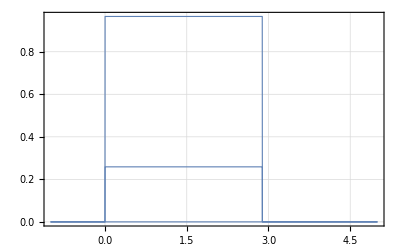

```mathematica
RadPlotOptions[];
Plot[radFld[final, "m", {5,y, 5}], {y, -1, 5}]
```

```mathematica
(* 2 segments of the Halbach array by hand *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 10
mx1 = Cos[φ+dφ/2]
my1 =Sin[φ+dφ/2]
mz1 = 0

(* create first segment, place same shape at z=0, z=R *)
segment1 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment1 = Append[segment1, {segment1[[1]][[1]], R}]

(* Iterate on the variables for the second segment *)
φ += dφ
mx2 = Cos[φ+dφ/2]
my2 =Sin[φ+dφ/2]
mz2 = 0

(* add new segments at z=0, z=R *)
segment2 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment2 = Append[segment2, {segment2[[1]][[1]], R}]
Print["segment is now: ", segment2]

(* first attempt to create segments, then define group for segments *)
s1 = radObjMltExtPgn[segment1, {mx1, my1, mz1}]
s2 = radObjMltExtPgn[segment2, {mx2, my2, mz2}]
group = radObjCnt[{s1, s2}]


(* color the object *)
radObjDrwAtr[group, {0, 0.5, 0.8}]

(* plot + show the object *)
RadPlot3DOptions[];
s = radObjDrw[group];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

π/6

1/(√2)

1/(√2)

0

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0}}

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

segment is now: {{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

6

8

9

9

-Graphics3D-

```mathematica
(* Plot the magnetic field's x-component *)
```

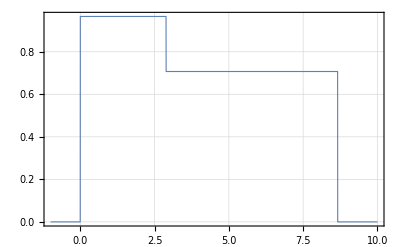

```mathematica
RadPlotOptions[];
Plot[radFld[group, "mx", {5,y, 5}], {y, -1, 10}]
```

```mathematica
(* Draw all 12 segments of the array, outward pointing magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[φ+dφ/2];
my =Sin[φ+dφ/2];
mz = 0;

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

25.4

10

-Graphics3D-

```mathematica
(* Create new Halbach array with spatially rotating magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
θ=π/12
dθ = π/2
(* outer radius *)
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[θ];
my =Sin[θ];
mz = 0;

Print["Magnetization angle for ", i," is: ", θ];

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;
θ+=dφ + dθ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

π/12

π/2

25.4

35

Magnetization angle for 1 is: π/12

Magnetization angle for 2 is: (3 π)/4

Magnetization angle for 3 is: (17 π)/12

Magnetization angle for 4 is: (25 π)/12

Magnetization angle for 5 is: (11 π)/4

Magnetization angle for 6 is: (41 π)/12

Magnetization angle for 7 is: (49 π)/12

Magnetization angle for 8 is: (19 π)/4

Magnetization angle for 9 is: (65 π)/12

Magnetization angle for 10 is: (73 π)/12

Magnetization angle for 11 is: (27 π)/4

Magnetization angle for 12 is: (89 π)/12

-Graphics3D-

```mathematica
(* Plot the y-component of the magnetic field to demonstrate spatial rotation *)
```

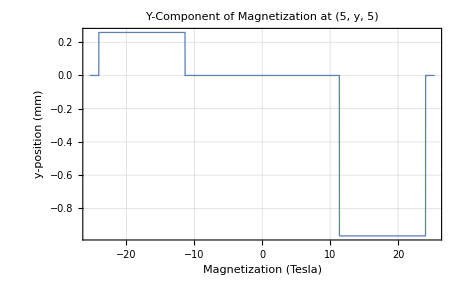

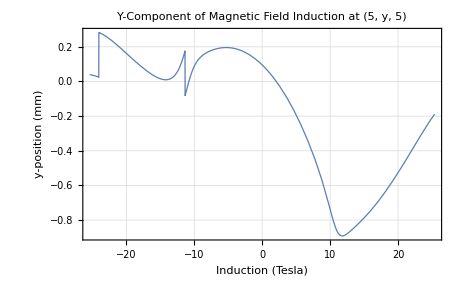

```mathematica
RadPlotOptions[];
Plot[radFld[halbach, "my", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetization at (5, y, 5)", AxesLabel->{"Magnetization (Tesla)", "y-position (mm)"}]
Plot[radFld[halbach, "By", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetic Field Induction at (5, y, 5)", AxesLabel->{"Induction (Tesla)", "y-position (mm)"}]
```

```mathematica
(* Plot the B-field *)
```

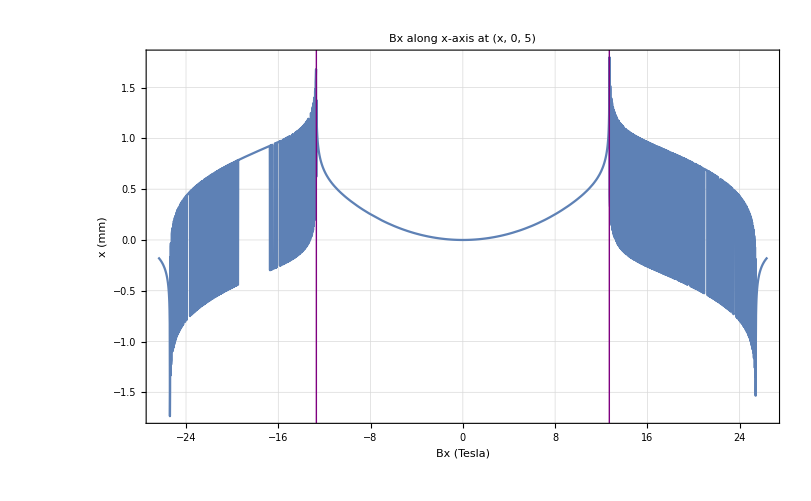

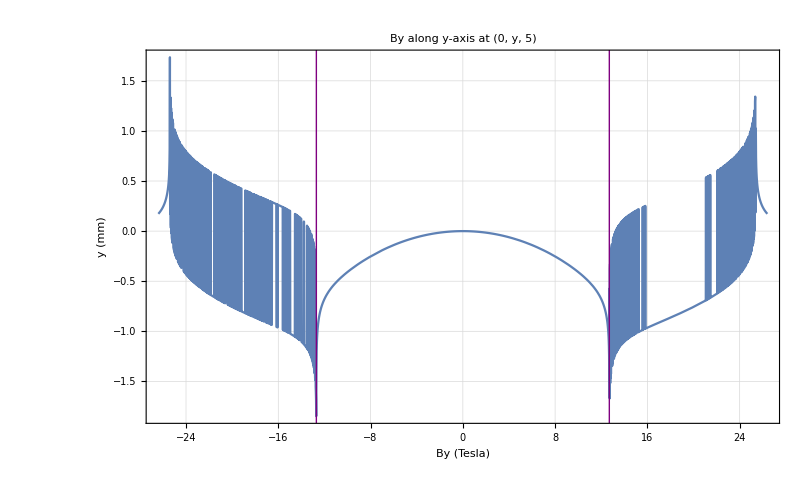

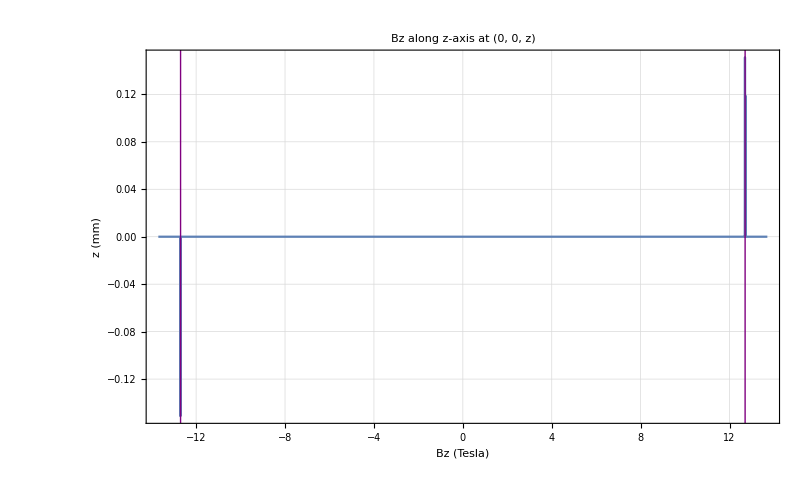

```mathematica
lineStyle={Thick,Purple};

(* draw lines at boundary of the inner radius *)
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[radFld[halbach, "Bx", {x, 0, 5}], {x, -R -1, R + 1}, PlotLabel->"Bx along x-axis at (x, 0, 5)", AxesLabel->{"Bx (Tesla)", "x (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "By", {0, y, 5}], {y, -R -1, R + 1}, PlotLabel->"By along y-axis at (0, y, 5)", AxesLabel->{"By (Tesla)", "y (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "Bz", {0, 0, z}], {z, -R/2  - 1, R/2 + 1}, PlotLabel->"Bz along z-axis at (0, 0, z)", AxesLabel->{"Bz (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle], Line[{{-R/2, -10}, {-R/2, 10}}], Line[{{R/2, -10}, {R/2, 10}}]}]
```

```mathematica
(* Plot the norm of the B-field *)
```

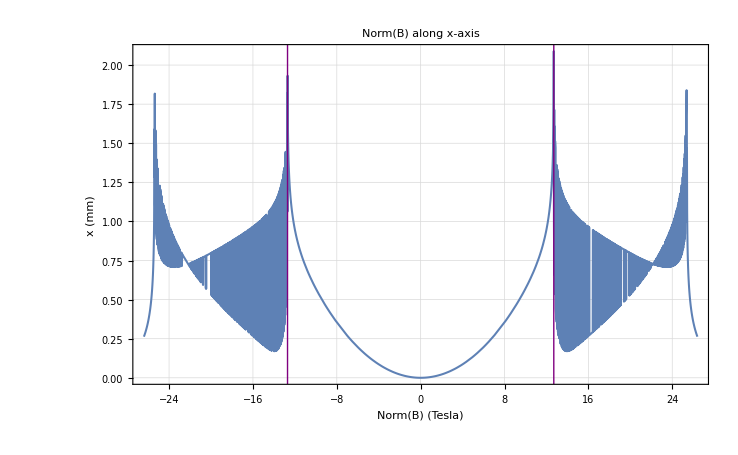

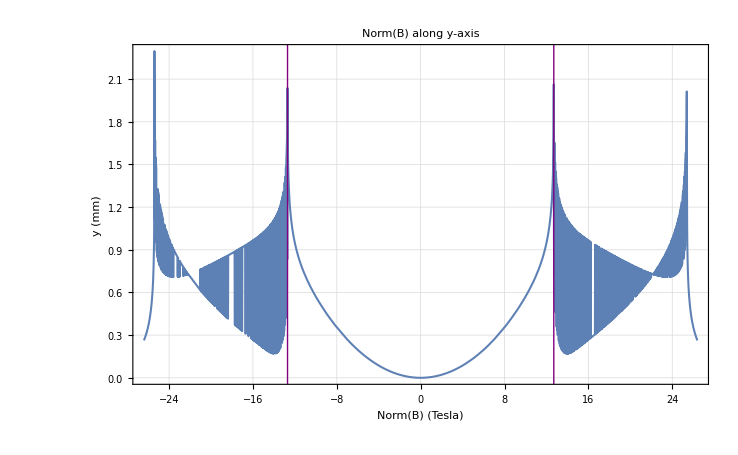

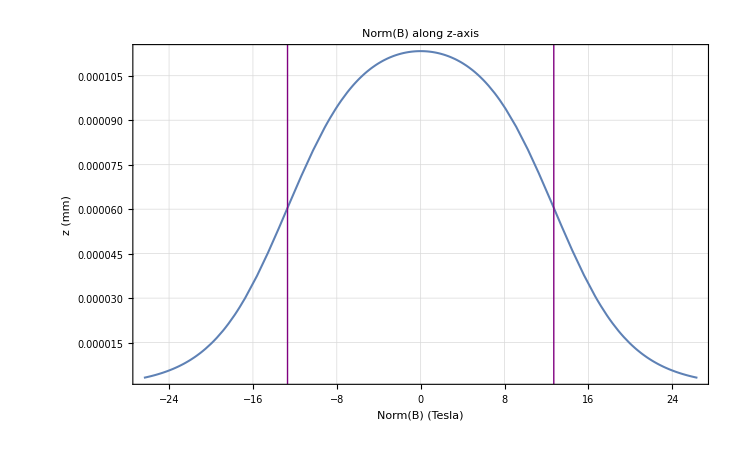

```mathematica
(* define norm function *)
norm [x_, y_, z_]:= Module[{bx, by, bz}, 
bx = radFld[halbach, "Bx", {x, y, z}];
by = radFld[halbach, "By", {x, y, z}];
bz = radFld[halbach, "Bz", {x, y, z}];
Return[Sqrt[bx^2 + by^2 + bz^2]];
]

lineStyle={Thick,Purple};
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[norm[x, 0, 5], {x, -R-1, R+1}, PlotLabel->"Norm(B) along x-axis", AxesLabel->{"Norm(B) (Tesla)", "x (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0, y, 5], {y,-R-1, R+1}, PlotLabel->"Norm(B) along y-axis", AxesLabel->{"Norm(B) (Tesla)", "y (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0.1, 0.1, z], {z, -R - 1, R+ 1}, PlotLabel->"Norm(B) along z-axis", AxesLabel->{"Norm(B) (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle],Line[{{-R/2,-10},{-R/2,10}}],Line[{{R/2,-10},{R/2,10}}]}]
```

```mathematica
(* Make a matrix of the B-field values for use with Python, export to a .csv file *)
```

```mathematica
(* initialize variables *)
xStart = -R/2;
yStart = -R/2;
zStart = -R/2;
m=3;
bxMatrix = {};
byMatrix = {};
bzMatrix = {};
normbMatrix = {};
bMatrix = {};

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bxMatrix=Append[bxMatrix, {}];
For[j=1, j≤ m, j++,
bxMatrix[[i]]=Append[bxMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bxMatrix[[i]][[j]]=Append[bxMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "Bx", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
byMatrix=Append[byMatrix, {}];
For[j=1, j≤ m, j++,
byMatrix[[i]]=Append[byMatrix[[i]], {}];
For[k=1,k≤ m, k++,
byMatrix[[i]][[j]]=Append[byMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "By", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
bzMatrix=Append[bzMatrix, {}];
For[j=1, j≤ m, j++,
bzMatrix[[i]]=Append[bzMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bzMatrix[[i]][[j]]=Append[bzMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "Bz", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
normbMatrix=Append[normbMatrix, {}];
For[j=1, j≤ m, j++,
normbMatrix[[i]]=Append[normbMatrix[[i]], {}];
For[k=1,k≤ m, k++,
normbMatrix[[i]][[j]]=Append[normbMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
norm[xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)]]
];
];
];

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bMatrix=Append[bMatrix, {}];
For[j=1, j≤ m, j++,
bMatrix[[i]]=Append[bMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bMatrix[[i]][[j]]=Append[bMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "B", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

Print["bxMatrix: ", MatrixForm[bxMatrix]]
Print["byMatrix: ", MatrixForm[byMatrix]]
Print["bzMatrix: ", MatrixForm[bzMatrix]]
Print["normbMatrix: ", MatrixForm[normbMatrix]]
Print["bMatrix: ", MatrixForm[bMatrix]]

SetDirectory["/Users/andrewwinnicki/Desktop/andrew/2019-2020/Doyle Lab/Modeling Project/B-Matrix"];
Export["bxMatrix.fits",bxMatrix];
Export["byMatrix.fits",byMatrix];
Export["bzMatrix.fits",bzMatrix];
Export["normbMatrix.fits",normbMatrix];
Export["bMatrix.fits",bMatrix];
```

bxMatrix: ((-0.458163
-0.23192
0.248943) | (1.80468
3.77605
1.56929) | (0.103985
-0.498683
0.103985)
(-1.74361
-3.71869
-2.33097) | (0.153093
-0.474294
-0.232813) | (-1.84866
-3.58521
-1.08112)
(0.103985
-0.498683
0.103985) | (1.56044
3.25022
1.86921) | (-0.458163
-0.23192
-0.458163))

byMatrix: ((0.458163
0.23192
-0.248943) | (1.7096
3.77947
2.10077) | (-0.103985
0.498683
-0.103985)
(-1.65468
-4.39846
-2.43637) | (-0.056036
-0.0883883
0.209129) | (-2.49206
-4.56613
-1.74603)
(-0.103985
0.498683
-0.103985) | (2.05093
3.72271
2.1616) | (0.458163
0.23192
0.458163))

bzMatrix: ((1.10462×10^-11
2.02883×10^-11
1.50119×10^-11) | (-3.82649
2.99713×10^-11
3.96174) | (0.201604
-3.06392×10^-12
-0.201604)
(3.81027
2.8761×10^-11
-3.90883) | (2.00492×10^-11
2.20358×10^-11
-2.6598×10^-11) | (-3.91931
2.72484×10^-11
3.88932)
(-0.201604
1.17291×10^-12
0.201604) | (3.98893
-7.89528×10^-13
-3.63363) | (-5.60027×10^-12
6.47127×10^-12
2.43163×10^-11))

normbMatrix: ((0.647941
0.327984
0.352059) | (5.14968
5.53396
5.00731) | (0.249539
0.705244
0.249539)
(4.48263
4.88547
4.8214) | (0.144424
0.241481
0.211617) | (4.76219
5.34656
4.28793)
(0.249539
0.705244
0.249539) | (5.00975
5.13362
4.69496) | (0.647941
0.327984
0.647941))

bMatrix: ((-0.458163 | 0.458163 | 1.22646×10^-11
-0.23192 | 0.23192 | 2.02884×10^-11
0.248943 | -0.248943 | 3.01265×10^-11) | (1.7379 | 1.60568 | -3.82117
4.42431 | 3.52664 | 2.55948×10^-11
2.16266 | 2.13606 | 3.9393) | (0.103985 | -0.103985 | 0.201604
-0.498683 | 0.498683 | -5.4844×10^-12
0.103985 | -0.103985 | -0.201604)
(-1.61766 | -1.62413 | 3.81264
-3.45725 | -4.33449 | 2.51742×10^-11
-2.19345 | -2.04325 | -3.829) | (0.120741 | 0.209129 | 1.88515×10^-11
0.273834 | -0.362222 | 2.20359×10^-11
-0.0647048 | -0.418258 | -2.80674×10^-11) | (-1.70938 | -1.56426 | -3.89217
-3.56802 | -4.44696 | 2.65006×10^-11
-1.71601 | -2.01288 | 3.85329)
(0.103985 | -0.103985 | -0.201604
-0.498683 | 0.498683 | -5.94587×10^-13
0.103985 | -0.103985 | 0.201604) | (1.71595 | 2.22756 | 4.10868
3.44881 | 3.30083 | 2.01405×10^-12
1.98591 | 2.3652 | -3.62565) | (-0.458163 | 0.458163 | -1.83807×10^-11
-0.23192 | 0.23192 | 6.47118×10^-12
-0.458163 | 0.458163 | -6.33398×10^-12))